# Лабораторная работа 6. Работа с файлами.

## Задание 1.

Реализуйте самостоятельно алгоритм факторизации целых чисел методом грубой силы (перебор делителей).
Проведите исследование скорости работы.
Улучшите скорость работы алгоритма при непосредственном вызове, проведя необходимую предварительную подготовку. Вычислите результаты функции предварительно и запишите их в файл. После этого, вычислять заново нужно только те, разложения, которых нет в файле.
Проведите исследование скорости работы улучшенного алгоритма.

```mathematica
(*Разбираюсь с алгоритмом*)
(*Производится перебор всех целых чисел от 2 до квадратного корня из факторизуемого числа n и в вычислении остатка от деления n на каждое из этих чисел. Если остаток от деления на некоторое число m равен нулю,то m является делителем n. В этом случае n сокращается на m и процедура повторяется.По достижении квадратного корня из оставшегося числа и невозможности сократить его ни на одно из меньших чисел,оно объявляется простым и также приписывается к простым сомножителям исходного числа n*)
```

```mathematica
n=12234;
i=2;
While[i<Sqrt[n],If[Head[n/i]===Integer,n=n/i;Print[i],Nothing];i++]
Print[n]
```

2

3

2039

```mathematica
factorize[n_]:=Block[{i=2,list={},tempN=n},While[i<Sqrt[tempN],If[Head[tempN/i]===Integer,list=Append[list,i];tempN=tempN/i,Nothing];i++];list=Append[list,tempN];Return[list]]
```

```mathematica
factorize[15556]
```

{2,7778}

```mathematica
Timing[factorize[1234563567]]
Timing[factorize[12345635645]]
Timing[factorize[123456356456]]
Timing[factorize[1234563564561]]
```

{0.078125,{3,61,6746249}}

{0.15625,{5,7,3881,90887}}

{0.015625,{2,4,23,61,137,80287}}

{27.125,{3,59,6974935393}}

```mathematica
(*Разбираюсь*)
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
testl={1,2,3,4}
```

{1,2,3,4}

```mathematica
Export["test.txt",testl]
(*Exports data to a file, converting it to the format corresponding to the file extension*)
```

test.txt

```mathematica
templ=Import["test.txt"]
```

1
2
3
4

```mathematica
templ//Head
```

String

```mathematica
StringSplit[templ]
```

{1,2,3,4}

```mathematica
(*Как строку*)
Export["test.txt",testl,"String"]
```

test.txt

```mathematica
templ=Import["test.txt"]
templ//Head
```

{1, 2, 3, 4}

String

```mathematica
(*Обратно в выражение*)
ToExpression@templ
%//Head
```

{1,2,3,4}

List

```mathematica
Export["test.dat",testl]
```

test.dat

```mathematica
Import["test.dat"]//Flatten
```

{1,2,3,4}

## Задание 2.

Реализуйте функцию, которая выводит список файлов в некоторой директории. 
1. Упорядоченный по названию файла.
2. Упорядоченный по расширению файла.
3. Упорядоченный по размеру файла.

Важно! Изучите единицы измерения размера файла в WM. Они могут вас удивить.
https://ru.wikipedia.org/wiki/%D0%9C%D0%B5%D0%B1%D0%B8%D0%B1%D0%B0%D0%B9%D1%82

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
(*Lists all files in the current working directory.*)
files=FileNames[];
```

```mathematica
files
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb}

```mathematica
sortByName[list_]:=Sort[list]
sortByName[files]
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb}

```mathematica
UnitConvert[FileSize[#],"Kibibytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Bytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Mebibytes"]&/@FileNames[]
```

{3992.41 KiB,228.197 KiB,4.66406 KiB}

{4.08823×10^6 B,233674. B,4776. B}

{3.89884 MiB,0.222849 MiB,0.00455475 MiB}

## Задание 3.

Реализуйте возможность ограничения регулярности вызова функции (возьмите любую из предыдущих ЛР).
Функция должна вызываться не чаще, чем раз в 30 секунд (или любой другой интервал). Для этого стоит хранить историю времени вызовов функции в файле.

## Задание 4.

Запишите в файл своеобразную таблицу интегралов, вычисленную в WM с помощью встроенной функции.
После этого реализуйте функция, которая считает интегралы, используя ваш файл.

```mathematica
f=x^2;
```

```mathematica
Integrate[f,x]
```

x^3/3

## Задание 5.

Реализуйте функцию, для генерации текстового файла, некоторого размера.
Файл состоит из случайных (безсвязных) слов английского алфавита записанных по строкам. 
Функция принимает на вход: 
Максимальный размер строки (клоичество слов в сторке).
Максимальную длину одного слова.
Точный размер в Мегабайтах (Мебибайтах).

Обеспечьте возможность котнроля текущего статуса работы с помощью функции Monitor[].

Реализуйте возможность выбора языка слов*

Указание! Файл следует записывать построчно, используя функции для поточной записи при этом, контролируя текущий размер файла. Размер файла коррелирует с размером строки.

```mathematica
characters=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
randomword[n_]:=StringJoin@RandomSample[characters,n]
```

```mathematica
randomword[10](*пример слова*)
```

uvchjlwpyr

```mathematica
StringRiffle[Table[randomword[RandomInteger[{3,10}]],RandomInteger[{5,20}]]](*строка файла*)
```

gysdtzbe icxbu wlvnt dyak zpv cxukwyaj obaxg taql wohilt onktswug seyqrtm huc uialfhtdp vtuyk sef uirf mubvrifkot

## Задание 6.

Пусть задан текстовый файл. В нём записаны слова (одна строка файла - одно слово). Реализуйте возможность удаления повторяющихся слов в файле. 
Считывать весь файл целиком нельзя! Используйте поточное считывание\запись.

## Задание 7.

Пусть задан текстовый файл. В нём записаны слова (слова разделены запятой и пробелом). Представьте файл, хранящий те же слова, но в отсортированном виде.

## Задание 8.

Используя файл covid_history.csv выполните следующие задачи. 
1. Графически интерпретируйте данные, предварительно их обработав.
2. Проверьте выполнение закона Бенфорда для определённой страны или всех данных сразу. 
3. Записшите в новый файл, какая страна лидировала по количеству заболевших в каждый из дней.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["covid_history.csv"];
```

```mathematica
data⟦All,5⟧
```

{Albania,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,2.,10.,12.,23.,33.,38.,42.,51.,55.,59.,64.,70.,76.,89.,104.,123.,146.,174.,186.,197.,212.,223.,243.,259.,277.,304.,333.,361.,377.,383.,400.,409.,416.,433.,446.,467.,475.,494.,518.,539.,548.,562.,584.,609.,634.,663.,678.,712.,726.,736.,750.,766.,773.,782.,789.,795.,803.,820.,832.,842.,850.,856.,868.,872.,876.,880.,898.,916.,933.,946.,948.,949.,964.,969.,981.,989.,998.,1004.,1029.,1050.,1076.,1099.,1122.,1137.,1143.,1164.,1184.,1197.,1212.,1232.,1246.,1263.,1299.,1341.,1385.,1416.,1464.,1521.,1590.,1672.,1722.,1788.,1838.,1891.,1962.,1995.,2047.,2114.,2192.,2269.,2330.,2402.,2466.,2535.,2580.,2662.,2752.,2819.,2893.,2964.,3038.,3106.,3188.,3278.,3371.,3454.,3571.,3667.,3752.,3851.,3906.,4008.,4090.,4171.,4290.,4358.,4466.,4570.,4637.,4763.,4880.,4997.,5105.,5197.,5276.,5396.,5519.,5620.,5750.,5889.,6016.,6151.,6275.,6411.,6536.,6676.,6817.,6971.,7117.,7260.,7380.,7499.,7654.,7812.,7967.,8119.,8275.,8427.,8605.,8759.,8927.,9083.,9195.,9279.,9380.,9513.,9606.,9728.,9844.,9967.,10102.,10255.,10406.,10553.,10704.,10860.,11021.,11185.,11353.,11520.,11672.,11816.,11948.,12073.,12226.,12385.,12535.,12666.,12787.,12921.,13045.,13153.,13259.,13391.,13518.,13649.,13806.,13965.,14117.,14266.,14410.,14568.,14730.,14899.,15066.,15231.,15399.,15570.,15752.,15955.,16212.,16501.,16774.,17055.,17350.,17651.,17948.,18250.,18556.,18858.,19157.,19445.,19729.,20040.,20315.,20634.,20875.,21202.,21523.,21904.,22300.,22721.,23210.,23705.,24206.,24731.,25294.,25801.,26211.,26701.,27233.,27830.,28432.,29126.,29837.,30623.,31459.,32196.,32761.,33556.,34300.,34944.,35600.,36245.,36790.,37625.,38182.,39014.,39719.,40501.,41302.,42148.,42988.,43683.,44436.,45188.,46061.,46863.,47742.,48530.,49191.,50000.,50637.,51424.,52004.,52542.,53003.,53425.,53814.,54317.,54827.,55380.,55755.,56254.,56572.,57146.,57727.,58316.,58316.,58991.,59438.,59623.,60283.,61008.,61705.,62378.,63033.,63595.,63971.,64627.,65334.,65994.,66635.,67216.,67690.,67982.,68568.,69238.,69916.,70655.,71441.,72274.,72812.,73691.,74567.,75454.,76350.,77251.,78127.,78992.,79934.,80941.,81993.,83082.,84212.,85336.,86289.,87528.,88671.,89776.,90835.,91987.,93075.,93850.,94651.,95726.,96838.,97909.,99062.,100246.,101285.,102306.,103327.,104313.,105229.,106215.,107167.,107931.,108823.,109674.,110521.,111301.,112078.,112897.,113580.,114209.,114840.,115442.,116123.,116821.,117474.,118017.,118492.,118938.,119528.,120022.,120541.,121200.,121544.,121847.,122295.,122767.,123216.,123641.,124134.,124419.,124723.,125157.,125506.,125842.,126183.,126531.,126795.,126936.,127192.,127509.,127795.,128155.,128393.,128518.,128752.,128959.,129128.,129307.,129456.,129594.,129694.,129842.,129980.,130114.,130270.,130409.,130537.,130606.,130736.,130859.,130977.,131085.,131185.,131238.,131276.,131327.,131419.,131510.,131577.,131666.,131723.,131753.,131803.,131845.,131890.,131939.,131978.,132015.,132032.,132071.,132095.,132118.,132153.,132176.,132209.,132215.,132229.,132244.,132264.,132285.,132297.,132309.,132315.,132337.,132351.,132360.,132372.,132374.,132379.,132384.,132397.,132415.,132426.,132437.,132449.,132459.,132461.,132469.,132476.,132481.,132484.,132488.,132490.,132490.,132496.,132497.,132499.,132506.,132509.,132512.,132513.,132514.,132521.,132523.,132526.,132534.,132535.,132537.,132544.,132557.,132565.,132580.,132587.,132592.,132597.,132608.,132616.,132629.,132647.,132665.,132686.,132697.,132740.,132763.,132797.,132828.,132853.,132875.,132891.,132922.,132952.,132999.,133036.,133081.,133121.,133146.,133211.,133310.,133442.,133591.,133730.,133912.,133981.,134201.,134487.,134761.,135140.,135550.,135947.,136147.,136598.,137075.,137597.,138132.,138790.,139324.,139721.,140521.,141365.,142253.,143174.,144079.,144847.,145333.,146387.,147369.,148222.,149117.,150101.,150997.,151499.,152239.,153318.,154316.,155293.,156162.,157026.,157436.,158431.,159423.,160365.,161324.,162173.,162953.,163404.,164276.,165096.,165864.,166690.,167354.,167893.,168188.,168782.,169462.,170131.,170778.,171327.,171794.,171794.,172618.,173190.,173723.,174168.,174643.,174968.,175163.,175664.,176172.,176667.,177108.,177536.,177971.,178188.,178804.,179463.,180029.,180623.,181252.,181696.,181960.,182610.,183282.,183873.,184340.,184887.,185300.,185497.,186222.,186793.,187363.,187994.,187994.,189125.,189355.,190125.,190815.,191440.,192013.,192600.,193075.,193269.,193856.,194472.,195021.,195523.,195988.,195988.,196611.,197167.,197776.,198292.,198732.,199137.,199555.,199750.,199945.,200173.,200639.,201045.,201402.,201730.,201902.,202295.,202641.,202863.,203215.,203524.,203787.,203925.,204301.,204627.,204928.,205224.,205549.,205777.,205897.,206273.,206616.,206935.,207221.,207542.,207709.,207709.,208352.,208899.,208899.,210224.,210224.,210885.,210885.,212021.,212021.,213257.,214905.,214905.,219694.,220487.,222664.,224569.,226598.,228777.,230940.,232637.,233654.,236486.,239129.,241512.,244182.,246412.,248070.,248070.,248859.,251015.,252577.,254126.,254126.,255741.,258543.,258543.,261240.,261240.,263172.,263172.,264624.,264875.,265716.,266416.,267020.,267020.,267551.,268008.,268304.,268491.,268940.,269301.,269601.,269904.,270164.,270370.,270455.,270734.,270947.,271141.,271141.,271527.,271563.,271702.,271825.}

```mathematica
Position[data,"Ukraine"]
```

{{1,215}}

```mathematica
Position[data,"Belarus"]
```

{{1,22}}

```mathematica
valuesBel=data⟦All,22⟧/.""->0//Rest;
```

```mathematica
valuesUkr=data⟦All,215⟧/.""->0//Rest;
```

```mathematica
dates=FromDateString[#]&/@(data⟦All,1⟧//Rest);
```

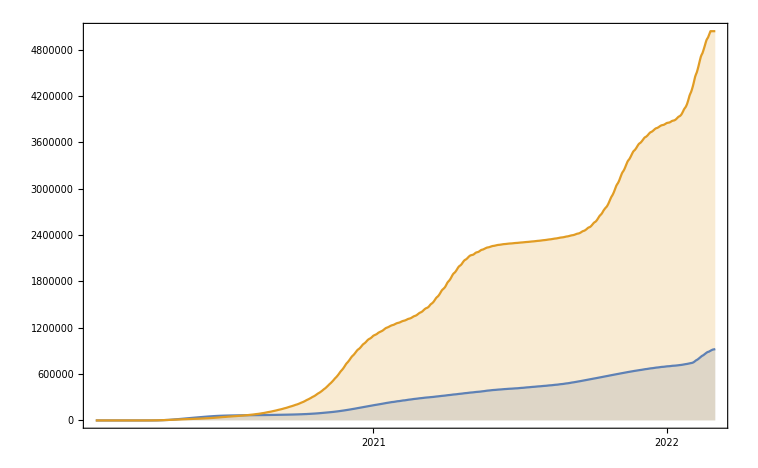

```mathematica
DateListPlot[{MapThread[{#1,#2}&,{dates,valuesBel}],MapThread[{#1,#2}&,{dates,valuesUkr}]},Filling->Bottom]
```